```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
Themes`AddThemeRules["tol",Method->{DefaultPlotStyle->{Directive[{blue,Thick}],Directive[{red,Thick,Dashed}],Directive[{green,Thick,Dotted}],Directive[{yellow,Thick,DotDashed}],Directive[redpurple],Directive[purpleblue],Directive[grey],Directive[Black],Directive[blue]}},AxesStyle->Directive[Black,myfontsize,Thickness[1/500],FontFamily->Auto],FrameStyle->Directive[Black,myfontsize,Thickness[1/500],FontFamily->Auto](*,LabelStyle->18,AxesStyle->White,TicksStyle->LightGray,Background->Gray*)];
$PlotTheme="tol";
```

```mathematica
dat1e3=Table[Import["iteration_a1e3_"<>ToString[i]<>".csv"],{i,19}];
```

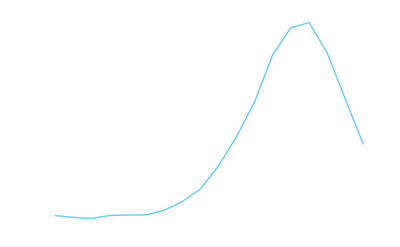

```mathematica
ListPlot[Table[Std[dat1e3[[i]][[;;,2]]],{i,18}],Joined->True,Axes->None,Frame->Auto,FrameLabel->{"# genes","std of mutual info"},ImageSize->a5rsize]
```

```mathematica
expdf["std_minfo_a1e3",%]
```

std_minfo_a1e3.pdf

```mathematica
datad=Table[Import["iteration_admax_"<>ToString[i]<>".csv"],{i,25}];
```

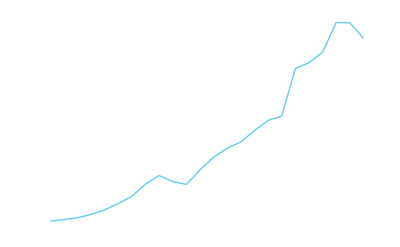

```mathematica
ListPlot[Table[Std[datad[[i]][[;;,2]]],{i,24}],Joined->True,Axes->None,Frame->Auto,FrameLabel->{"# genes","std of mutual info"},ImageSize->a5rsize]
```

```mathematica
expdf["std_minfo_admax",%]
```

std_minfo_admax.pdf

```mathematica
datac=Table[Import["iteration_afromc_"<>ToString[i]<>".csv"],{i,28}];
```

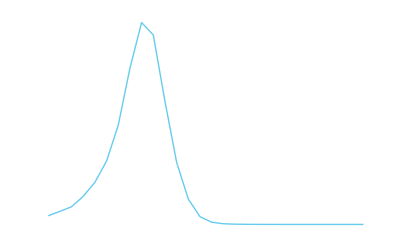

```mathematica
ListPlot[Table[Std[datac[[i]][[;;,2]]],{i,28}],Joined->True,Axes->None,Frame->Auto,FrameLabel->{"# genes","std of mutual info"},ImageSize->a5rsize]
```

```mathematica
expdf["std_minfo_afromc",%]
```

std_minfo_afromc.pdf

```mathematica
data0=Table[Import["iteration_a0_"<>ToString[i]<>".csv"],{i,7}];
```

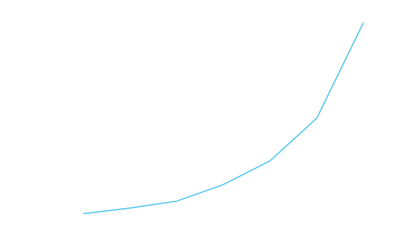

```mathematica
ListPlot[Table[Std[data0[[i]][[;;,2]]],{i,7}],Joined->True,Axes->None,Frame->Auto,FrameLabel->{"# genes","std of mutual info"},ImageSize->a5rsize]
```

```mathematica
expdf["std_minfo_afromc",%]
```

std_minfo_afromc.pdf

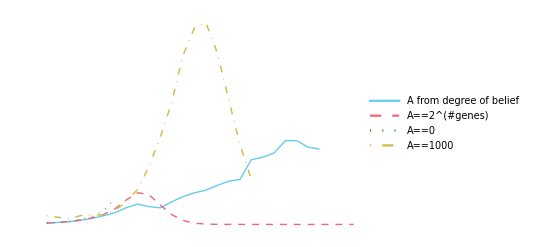

```mathematica
ListPlot[{Table[Std[datad[[i]][[;;,2]]],{i,25}],Table[Std[datac[[i]][[;;,2]]],{i,28}],
Table[Std[data0[[i]][[;;,2]]],{i,7}],
Table[Std[dat1e3[[i]][[;;,2]]],{i,19}]},Joined->True,Axes->None,Frame->Auto,FrameLabel->{"# genes","std of mutual info"},ImageSize->a5rsize,(*PlotStyle->{Auto,Dashed,Dotted},*)PlotLegends->Placed[{A " from degree of belief",A == 2^"#genes",A == 0,A == 1000},labelposition[{0.05,0.95}]],PlotRange->All]
```

```mathematica
expdf["comparison_std_minfo",%]
```

comparison_std_minfo.pdf

```mathematica
Log[2,6029]//N
```

12.5577

```mathematica
dato=Import["infoseq_afromc_28.csv"]
```

{{6,0.0013201},{57,0.00366211},{32,0.0073734},{66,0.0132599},{75,0.023237},{88,0.03897},{93,0.0602239},{22,0.089574},{14,0.117802},{21,0.132639},{43,0.123568},{89,0.0967005},{70,0.0653778},{90,0.0392137},{94,0.0217774},{30,0.0115567},{77,0.00595885},{85,0.0030284},{24,0.00152627},{27,0.000766231},{84,0.000383885},{23,0.000192118},{86,0.0000961032},{87,0.0000480626},{25,0.0000240259},{10,0.0000120096},{63,6.00325×10^-6},{54,3.00113×10^-6}}

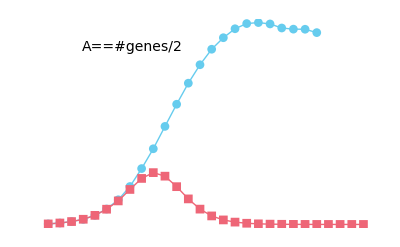

```mathematica
pstdListPlot[{dat[[;;,2]],dato[[;;,2]]},Axes->None,Frame->Auto,FrameLabel->{{"mutual info",None},{genes,None}},FrameTicks->{Auto,{T@{Range[1,Length@dato],Style[#,12]&/@dato[[;;,1]]},Auto}},ImageSize->a5rsize,Joined->True,PlotMarkers->Auto,Epilog->Text[Style[A=="#genes/2",14],Scaled[{0.3,0.9}],{0.3,0.9}]]
```

```mathematica
expdf["progression_AhalfC",%]
```

progression_AhalfC.pdf

```mathematica
Log[2,n]//N
```

12.5577

```mathematica
2^12
```

4096

```mathematica
2^10
```

1024

```mathematica
Binomial[94,10]//N
```

9.04126×10^12

```mathematica
n/2^10//N
```

5.8877

```mathematica
le=Min[Length/@{dat1e3,dat,dato}];{dat1e3[[;;le,1]],dat[[;;le,1]],dato[[;;le,1]]}//T//MF
```

(9 | 6 | 6
67 | 57 | 57
13 | 32 | 32
16 | 66 | 66
17 | 75 | 75
59 | 88 | 88
70 | 44 | 93
39 | 90 | 22
43 | 39 | 14
89 | 46 | 21
93 | 74 | 43
55 | 63 | 89
76 | 53 | 70
22 | 40 | 90
66 | 29 | 94)

```mathematica
dat1e3=Import["infoseq_a1e3_18.csv"]
```

{{9,0.00714047},{67,0.0127164},{13,0.0179127},{16,0.0227846},{17,0.0294803},{59,0.0361631},{70,0.0497722},{39,0.0759585},{43,0.120456},{89,0.19676},{93,0.30768},{55,0.458223},{76,0.646054},{22,0.850405},{66,1.0488},{8,1.21224},{92,1.32999},{21,1.40668}}

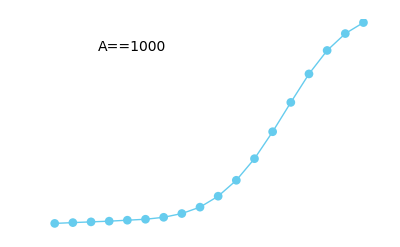

```mathematica
ListPlot[dat1e3[[;;,2]],Axes->None,Frame->Auto,FrameLabel->{{"mutual info",None},{genes,None}},FrameTicks->{Auto,{T@{Range[1,Length@dat1e3],Style[#,12]&/@dat1e3[[;;,1]]},Auto}},ImageSize->a5rsize,Joined->True,PlotMarkers->Auto,Epilog->Text[Style[A==1000,14],Scaled[{0.3,0.9}],{0.3,0.9}]]
```

```mathematica
expdf["progression_A1e3",%]
```

progression_A1e3.pdf

```mathematica
dat1e6=Import["infoseq_1000000_30.csv"]
```

{{9,8.99509×10^-6},{63,0.0000223753},{13,0.0000423247},{11,0.0000819628},{82,0.000152251},{83,0.000281068},{5,0.00047234},{1,0.000690619},{67,0.000820893},{53,0.000933726},{74,0.00103995},{16,0.00114339},{40,0.0012529},{54,0.00137422},{57,0.00154244},{51,0.00176335},{29,0.0020942},{66,0.00263217},{22,0.00342926},{70,0.00451066},{89,0.00582635},{77,0.00725472},{4,0.0086469},{20,0.00986983},{92,0.0108101},{93,0.0114654},{76,0.0118823},{27,0.0121235},{6,0.0122629},{94,0.0123454}}

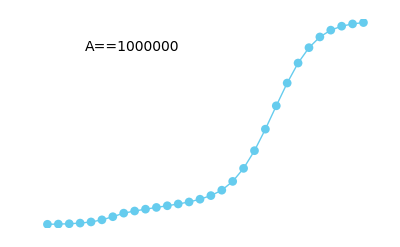

```mathematica
ListPlot[dat1e6[[;;,2]],Axes->None,Frame->Auto,FrameLabel->{{"mutual info",None},{genes,None}},FrameTicks->{Auto,{T@{Range[1,Length@dat1e6],Style[#,12]&/@dat1e6[[;;,1]]},Auto}},ImageSize->a5rsize,Joined->True,PlotMarkers->Auto,Epilog->Text[Style[A==10^6,14],Scaled[{0.3,0.9}],{0.3,0.9}]]
```

```mathematica
expdf["progression_A1e6",%]
```

progression_A1e6.pdf

```mathematica
{dato[[;;,1]],dat1000[[;;,1]],dat1e6[[;;,1]]}//MF
```

({6,57,32,66,75,88,93,22,14,21,43,89,70}
{9,67,13,16,17,59,70,39,43,89,93,55,76,22,66,8,92}
{9,63,13,11,82,83,5,1,67,53,74,16,40,54,57,51,29,66,22,70,89,77,4,20})

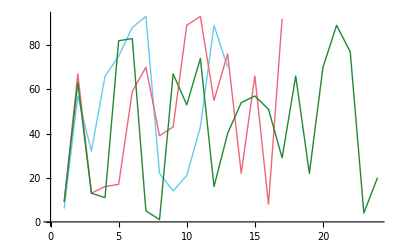

```mathematica
ListPlot[{dato[[;;,1]],dat1000[[;;,1]],dat1e6[[;;,1]]},Joined->True]
```